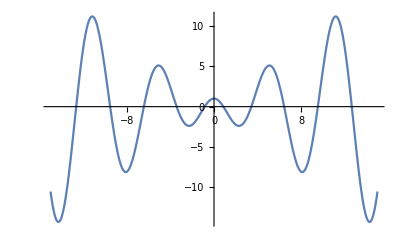

{x→0.860334}

```mathematica
Remove["Global`*"]
eqnlist={Cos[x]-x Sin[x]==0};
Plot[Cos[x]-x Sin[x],{x,-15,15}]
FindRoot[Cos[x]-x Sin[x],{x,1}]
```

InterpolatingFunction::dmval: Input value {-0.997937} lies outside the range of data in the interpolating function. Extrapolation will be used.

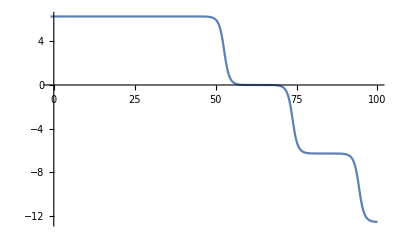

```mathematica
Remove["Global`*"]
eqnlist={x''[t] + ω0^2 Sin[x[t]] == 0,x[0]==A,x'[0]==0};
A = π;
ω0=1;
soln = NDSolve[eqnlist,x[t],{t,0,100}][[1]];
q[t_]=π+x[t]/.soln ;
Plot[q[t],{t,-1,100}]
```

```mathematica
Remove["Global`*"]
(*Teach Mathematic physics*)
$Assumptions={Element[{β,ω0,Ω,F0,A,t},Reals]&&β>0&&β<ω0&&ω0>0&&Ω>0&&F0>0&&A>0&&t>0};
(**********************************************************************************************)
(*Define differential equation*)
F[t_]=F0 Cos[Ω t];
osc[β_] = x''[t] + 2β x'[t]+ω0^2 x[t] == F[t];
(**********************************************************************************************)
(*Set up DSolve*)
diffeq[β_]={osc[β]};
iclist = {x[0]==x0, x'[0]==v0x};
eqnlist[β_] = Join[diffeq[β],iclist];
tlo = 0;
thi = 8;
soln[β_]=NDSolve[eqnlist[β],x[t],{t,tlo,thi}][[1]];
x[β_,t_]=x[t]/.soln[β];
(*Print["\nFor critically damping, x[t] = ",x[ω0,t],
"\notherwise x[t] = ",x[β,t]]
p1brule={x0->A,v0x->0,F0->0};
Print["\nFree osc x[t] = "x[0,t]/.p1brule]
Print["\nDamped osc x[t] = "x[β,t]/.p1brule]
Print["\nCrit damped osc x[t] = "x[ω0,t]/.p1brule]*)
(**********************************************************************************************)
(* Set up plot *)
(*Physical parameters*)
x0 = 1.;
v0x = 0;
ω0 = 2π;
Ω = 0.95 ω0;
F0 = 0.;
(*Plot parameters*)
range = {{-1,thi},1.2x0{-1,1}};
(**********************************************************************************************)
traj[β_]:= Plot[Evaluate[x[β,t]],{t,tlo,thi},PlotRange->range]
points[β_,t_]:= Graphics[{PointSize[0.03],Point[{0,x[β,t]}],
Red,PointSize[0.02],Point[{t,x[β,t]}]}]
pix[β_,t_]:= Show[traj[β],points[β,t]]
Manipulate[
Animate[pix[β,t],{t,tlo,thi},AnimationRunning->False,ControlPlacement->Top],{β,0,2ω0},ControlPlacement->Top
]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

ReplaceAll::reps: {ω0^2 x[t]+2 β x'[t]+x''[t]==F0 Cos[t Ω],x[0]==x0,x'[0]==v0x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Animate::vsform: Animate argument {t,tlo,thi} does not have the correct form for a variable specification.

General::stop: Further output of Animate::vsform will be suppressed during this calculation.

Animate::vsform: Animate argument {t,tlo,thi} does not have the correct form for a variable specification.

General::stop: Further output of Animate::vsform will be suppressed during this calculation.

```mathematica
Remove["Global`*"]
(*Teach Mathematic physics*)
$Assumptions={Element[{l,t,θ0},Reals]&&l>0&&g>0&&θ0>0};
g=9.82
(**********************************************************************************************)
(*Define differential equation*)
ω0 = √(g/l)
diffeq = θ
```